# Epicycles 研究笔记 3

### 使用离散点和离散傅里叶变换画出路径

### 方式一：2D图形绘制

```mathematica
g[pts_]:=DynamicModule[{if,p,len},if=InverseFourier[Complex@@@pts];len=Length@pts;Manipulate[p=Sum[if[[Mod[n+len,len]+1]]Exp[I t n],{n,-m,m}];Graphics[{Line@ReIm@Table[p,{t,0,2π,step}]}],{m,100,500,1},{step,{0.5,0.3,0.1,0.05,0.03,0.02,0.01},ControlType->Setter}]]
```

### 方式二：参数方程绘制

```mathematica
pp[pts_]:=DynamicModule[{if,cs},if=InverseFourier[Complex@@@pts];Manipulate[cs=Join[if[[-m;;]],if[[;;m+1]]];ParametricPlot[ReIm@Sum[cs[[n]]Exp[(n-m-1)I t],{n,2m+1}],{t,0,2π}],{m,100,500,1}]]
```

## 实例

#### 使用来自网络的参照图像

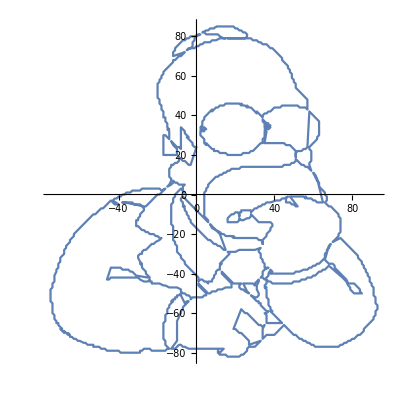

```mathematica
img=Import["http://www.qedcat.com/misc/homer1_clean_pixel.png"];
pts=PixelValuePositions[img, Black,0.05];
pts=Map[{-90,-90}+#&,pts];
elephantPlot=ListPlot[pts,AspectRatio->Automatic];
shortest=Last@FindShortestTour@pts;
pts=pts[[shortest]];
ListLinePlot[pts,AspectRatio->Automatic]
```

```mathematica
g[pts]
```

```mathematica
pp[pts]
```

先将变换结果整理成{-m,m}的形式，再转变成索引值

```mathematica
DynamicModule[{if,cs,len,k},len=Length@pts;k=Ceiling[len/2];if=InverseFourier[Complex@@@pts];
cs=Join[if[[k-len;;]],if[[;;k]]];Manipulate[ParametricPlot[ReIm@Sum[cs[[n+Floor[len/2]+1]]Exp[n I t],{n,-m,m}],{t,0,2π}],{m,100,k,1}]]
```

直接使用周期数与索引的关系

```mathematica
DynamicModule[{if,cs,len,k},len=Length@pts;if=Fourier[Complex@@@pts]; Manipulate[ParametricPlot[ReIm@Sum[if[[Mod[n+len,len]+1]]Exp[n I t],{n,-a,b}],{t,0,2π}],{a,100,Ceiling[len/2]-1,1},{b,0,Ceiling[len/2]-1,1}]]
```

### 意外效果

```mathematica
Fourier@l
```

{{7.77817+0. ⅈ,0.+0. ⅈ},{-0.353553-1.06066 ⅈ,-1.06066-1.06066 ⅈ},{-4.24264+0. ⅈ,2.12132+0. ⅈ},{-0.353553+1.06066 ⅈ,-1.06066+1.06066 ⅈ}}

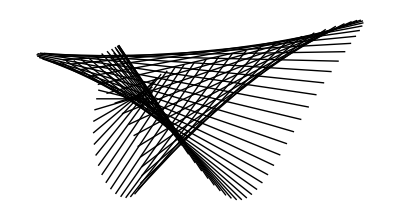

```mathematica
eg[Fourier@l]
```

```mathematica
eg3d[cs_]:=Block[{p=Sum[cs[[n]]Exp[I t If[EvenQ@n,n/2,-(n-1)/2]],{n,Length@cs}]},
Graphics3D[{Line@Table[Transpose@ReIm@p,{t,0,2π,0.05}]},RotationAction->"Clip"]]
```

```mathematica
l3d={{1,1,1},{2,5,2},{3,0,3},{5,5,5}};
ListLinePlot3D[l3d]
```

-Graphics3D-

```mathematica
eg3d[Fourier@l3d]
```

-Graphics3D-